```mathematica
ToRodRule[rule_]:=Join[MapThread[Rule,{Join[Prepend[2]/@Tuples[{0,1},2],Tuples[{0,1},3],Append[2]/@Tuples[{0,1},2]],IntegerDigits[rule-1,2,16]}],{{2,2,0}->2,{2,2,1}->2,{0,2,2}->2,{1,2,2}->2}]
```

```mathematica
Length@ToRodRule[0]-4
```

16

```mathematica
(*RodEvolution[rule_,n_,t_,init_:Automatic]:=CellularAutomaton[ToRodRule[rule],Replace[init,Automatic->Join[{2},ConstantArray[0,n],{2}]],t]*)

RodEvolution2[rule_,init_]:=Last@CellularAutomaton[ToRodRule[rule],init,1]
```

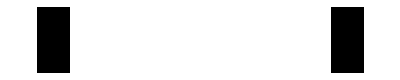

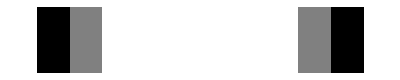

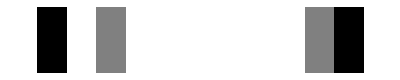

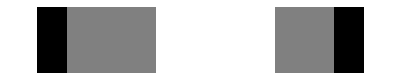

```mathematica
n=10;
start =Join[{2},RandomChoice[{0,1},n-2],{2}];
start = Join[{2},ConstantArray[0,n-2],{2}];
ArrayPlot[{start}]
update1 = RodEvolution2[50845,start];
ArrayPlot[{update1}]
grow1 = Join[{2,0},update1[[2;;-1]]]; (*Grow with a short state*)
ArrayPlot[{grow1}]
update2 = RodEvolution2[50845,grow1];
ArrayPlot[{update2}]
```

```mathematica
IntegerDigits[50-1,2,16]
```

{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1}

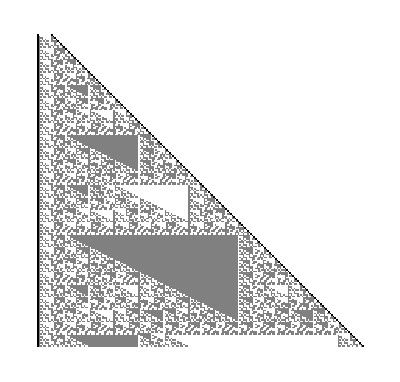

```mathematica
updates =NestList[RodEvolution2[50845,Join[{2,0},#[[2;;-1]]]]&,start,200];
ArrayPlot[updates]
```

```mathematica
updates =NestList[RodEvolution2[50845,Join[{2,0},#[[2;;-1]]]]&,start,2000];
ArrayPlot[updates]
```

-Graphics-

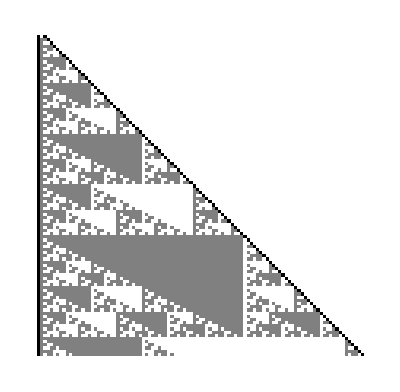

```mathematica
start={2,0,2};
updates =NestList[RodEvolution2[50845,Join[{2,0},#[[2;;-1]]]]&,start,100];
ArrayPlot[updates]
```

```mathematica
start={2,0,2};
numberofsamples = 10
ArrayPlot[#evol,PlotLabel->{#rule,#complexity}]&/@ReverseSortBy[Select[Table[With[{evol=NestList[RodEvolution2[rule,Join[{2,0},#[[2;;-1]]]]&,start,200]},<|"rule"->rule,"evol"->evol,"complexity"->StringLength@Compress[evol]|>],{rule,RandomInteger[2^16,numberofsamples]}],#complexity>1500&  ],#complexity&]
```

10

#### Find interesting ones with some constraints to help

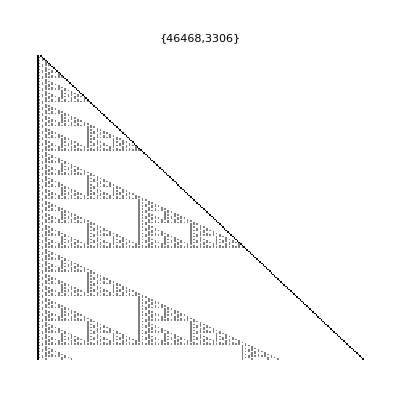
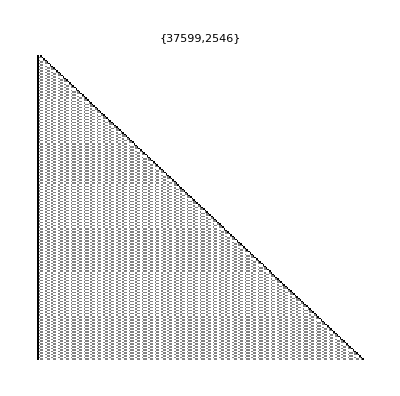
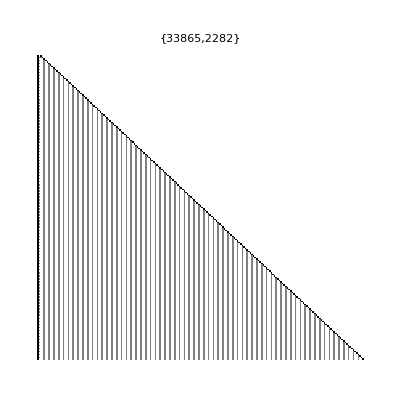
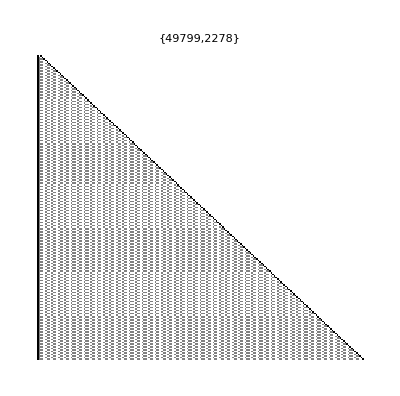
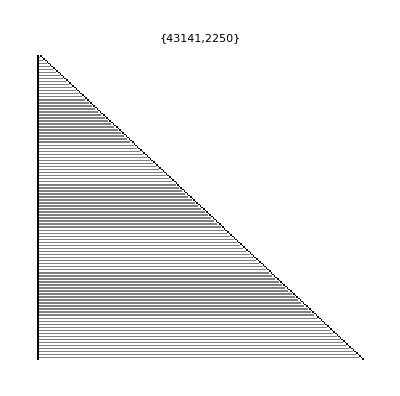
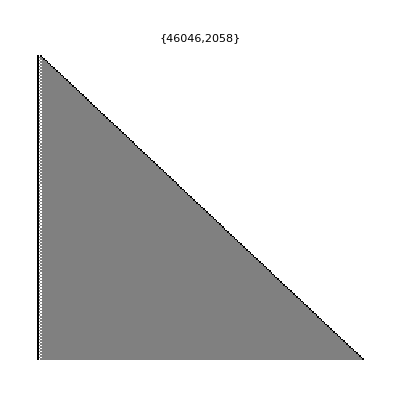
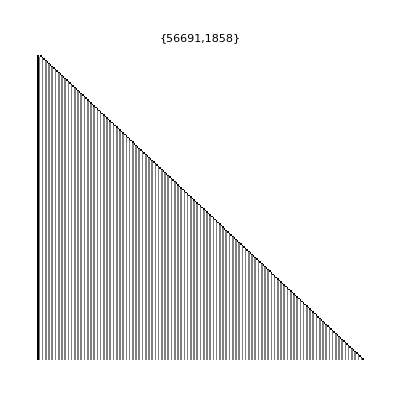
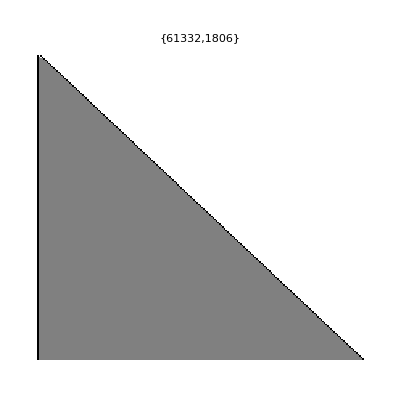

#### Interesting ones

```mathematica
i={1389,2671,2415,3612,2468,2883,5278,5278,6765,6984,10863,10516,10304,5279,14959,18283,51322,51864,54954,54251,33764,35241,35163,35306,38559,5305,39199,38971,42348,22188,22813,26475,26333,6910,41967,43884,46954,47944,47167,51051,51044,50152,50155,30700,31329,5803,34463,34667,60271,67437};
ii={1389,2671,2415,3612,2468,2883,5278,10516,10304,5279,14959,51322,51864,54954,54251,33764,35241,35163,35306,38559,5305,39199,38971,42348,22813,26475,26333,6910,41967,43884,46954,47944,47167,51051,51044,50152,30700,31329,5803,60271};
iii={46954,10304,22813,26475,33764,35306,51044,51051};
```

```mathematica
start={2,0,2};
numberofsamples = 10;
numberofevolutions = 4000;
var = 32;

all = Export["C:\\Users\\douwm\\repos\\wolfram_summer_school\\saved_results\\VeryLarge\\"<>ToString@#rule <>".png",ArrayPlot[#evol,PlotLabel->{#rule,#complexity}],ImageResolution->1000]&/@
ReverseSortBy[
Select[ParallelTable[With[{evol=NestList[RodEvolution2[rule,Join[{2,0},#[[2;;-1]]]]&,start,numberofevolutions]},<|"rule"->rule,"evol"->evol,"complexity"->StringLength@Compress[evol]|>],
{rule,iii}],
#complexity>5000 &&
1*numberofevolutions^2/2> Total[#evol,2]>2*numberofevolutions*2*1.3 &  ],#complexity&]
```

{C:\Users\douwm\repos\wolfram_summer_school\saved_results\VeryLarge\51051.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\VeryLarge\26475.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\VeryLarge\51044.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\VeryLarge\35306.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\VeryLarge\46954.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\VeryLarge\22813.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\VeryLarge\33764.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\VeryLarge\10304.png}

```mathematica
RulePlot[CellularAutomaton[ToRodRule@51051]]
```

RulePlot[CellularAutomaton[{{2,0,0}→1,{2,0,1}→1,{2,1,0}→0,{2,1,1}→0,{0,0,0}→0,{0,0,1}→1,{0,1,0}→1,{0,1,1}→1,{1,0,0}→0,{1,0,1}→1,{1,1,0}→1,{1,1,1}→0,{0,0,2}→1,{0,1,2}→0,{1,0,2}→1,{1,1,2}→0,{2,2,0}→2,{2,2,1}→2,{0,2,2}→2,{1,2,2}→2}]]

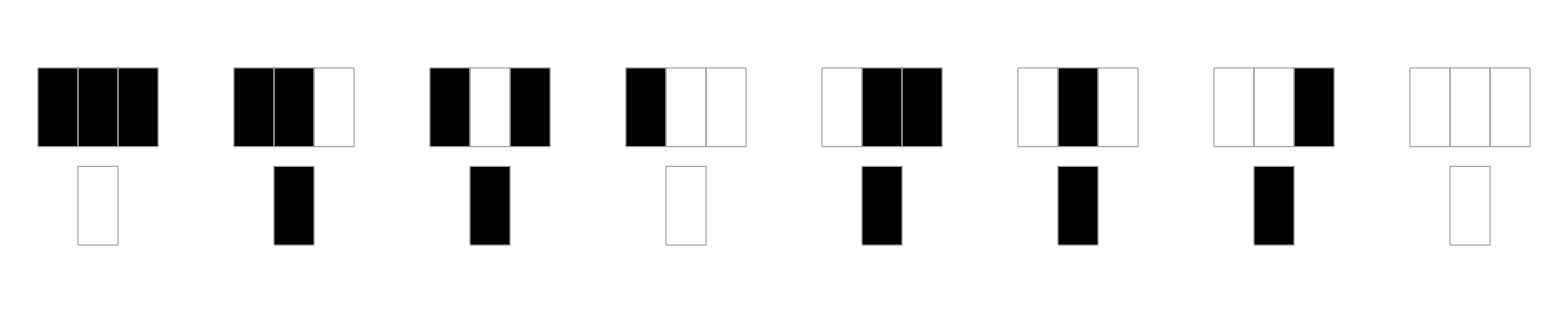

```mathematica
RulePlot[CellularAutomaton[110]]
```

#### Equivalent of CA110

```mathematica
rod110 = {{2,0,0}->1,{2,0,1}->1,{2,1,0}->0,{2,1,1}->0,{0,0,0}->0,{0,0,1}->1,{0,1,0}->1,{0,1,1}->1,{1,0,0}->0,{1,0,1}->1,{1,1,0}->1,{1,1,1}->0,{0,0,2}->0,{0,1,2}->0,{1,0,2}->0,{1,1,2}->0,{2,2,0}->2,{2,2,1}->2,{0,2,2}->2,{1,2,2}->2};
nevol = 100;
start={2,0,1,0,2};
evol = NestList[Last@CellularAutomaton[rod110,Join[{2,0},#[[2;;-1]]],1]&,start,nevol];
evol = PadLeft[evol];
ArrayPlot[evol[[2;;-2,3;;-3]]]
```

{{2,0,0}→1,{2,0,1}→1,{2,1,0}→0,{2,1,1}→0,{0,0,0}→0,{0,0,1}→1,{0,1,0}→1,{0,1,1}→1,{1,0,0}→0,{1,0,1}→1,{1,1,0}→1,{1,1,1}→0,{0,0,2}→0,{0,1,2}→0,{1,0,2}→0,{1,1,2}→0,{2,2,0}→2,{2,2,1}→2,{0,2,2}→2,{1,2,2}→2}

-Graphics-

```mathematica
|
```

```mathematica
evolca = CellularAutomaton[110,{{1},0},nevol];
ArrayPlot[evolca]
```

-Graphics-

```mathematica
evolrem2 = evol/. 2->0 ;
 evolrem2[[2;;-2,3;;-3]]==evolca[[3;;-1,All]]
```

True

```mathematica
evolca//Dimensions
evol//Dimensions
```

{501,501}

{501,505}

```mathematica
-Graphics--Graphics-
```

#### Have a close look at 10586

```mathematica
rule = 10586;
numberofevolutions = 20000;


res =With[{evol=NestList[RodEvolution2[rule,Join[{2,0},#[[2;;-1]]]]&,start,numberofevolutions]},<|"rule"->rule,"evol"->evol,"complexity"->StringLength@Compress[evol]|>];


ArrayPlot[#,PlotRange->{{1,All},{1,100}}]&/@Partition[PadRight[res["evol"]],numberofevolutions/10]
```

```mathematica
Row[ArrayPlot[#,PlotRange->{{1,All},{1,500}}]&/@Partition[PadRight[res["evol"]],numberofevolutions/10]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Have a close look at 37861

```mathematica
rule = 37861;
numberofevolutions = 20000;


res =With[{evol=NestList[RodEvolution2[rule,Join[{2,0},#[[2;;-1]]]]&,start,numberofevolutions]},<|"rule"->rule,"evol"->evol,"complexity"->StringLength@Compress[evol]|>];


ArrayPlot[#,PlotRange->{{1,All},{1,All}}]&@PadRight[res["evol"]]
```

-Graphics-

#### Look at 51051 with different init-cond

```mathematica
rule = 51051;
iii={rule};
start={2,0,1,2};
nstartrods = 100;
ninitconds = 24

initconds = Table[Join[{2},RandomChoice[{0,1},nstartrods],{2}],ninitconds]
numberofevolutions =4000;

all = Export["C:\\Users\\douwm\\repos\\wolfram_summer_school\\saved_results\\51051initcond\\100start\\"<>ToString@#init <>ToString@#rule <>".png",ArrayPlot[#evol,PlotLabel->{#rule,#init}],ImageResolution->1000]&/@

ParallelTable[With[{evol=NestList[RodEvolution2[rule,Join[{2,0},#[[2;;-1]]]]&,init,numberofevolutions]},<|"rule"->rule,"evol"->evol,"init"->init|>],
{init,initconds}]
ArrayPlot[#,PlotRange->{{1,All},{1,All}}]&@PadRight[res["evol"]]
```

24

{{2,1,1,0,0,0,0,1,0,1,1,0,0,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,0,0,0,0,1,0,0,1,1,0,1,1,0,0,0,1,1,0,0,1,1,1,1,1,1,0,0,1,1,1,1,0,0,1,1,0,1,0,0,0,0,0,1,1,1,1,1,1,1,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,1,1,1,0,0,1,2},{2,0,0,1,1,0,1,1,0,0,0,0,0,1,0,1,0,0,1,1,1,1,1,0,0,1,1,0,1,1,0,0,0,1,1,0,1,0,1,1,1,1,0,0,1,1,0,1,0,1,1,0,1,0,0,1,1,0,1,1,1,1,0,0,1,1,1,1,1,1,0,1,1,0,0,0,1,0,0,0,0,0,1,1,0,0,1,1,0,1,1,0,0,1,0,1,1,0,0,1,0,2},{2,1,1,1,1,1,1,0,0,0,0,1,1,1,1,0,1,0,1,0,1,0,0,0,1,1,1,1,1,0,0,1,0,1,0,0,1,0,0,1,0,0,0,1,1,0,0,0,1,1,1,0,1,1,1,0,0,1,1,1,1,0,0,0,1,1,1,0,0,0,1,1,1,1,1,1,1,1,0,1,1,0,0,1,1,0,0,0,1,0,1,1,1,0,1,1,0,1,1,0,1,2},{2,0,0,1,1,0,0,1,1,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,1,1,0,0,0,0,1,0,0,0,1,0,0,1,1,1,1,0,0,1,0,0,1,1,0,1,1,0,0,1,1,1,0,1,0,0,0,1,1,1,1,0,0,0,1,1,0,0,1,0,0,0,0,1,0,1,0,1,1,1,1,0,1,1,1,1,0,0,0,0,0,0,0,0,2},{2,0,0,1,0,0,0,0,0,1,1,1,0,1,1,0,0,0,0,0,1,1,1,0,1,1,1,1,1,1,0,0,1,1,1,1,1,0,0,0,0,1,0,1,0,1,0,0,1,0,1,0,0,1,1,1,1,0,0,0,1,0,0,0,1,1,1,1,1,1,1,1,1,0,1,0,1,1,0,0,1,1,0,0,1,1,0,1,0,1,1,0,1,1,1,1,0,0,1,1,0,2},{2,1,1,1,1,0,0,1,0,0,0,1,0,1,0,1,1,0,0,0,0,1,1,1,1,1,1,0,1,1,0,1,0,1,1,1,0,0,0,1,0,1,0,1,0,0,0,1,0,1,1,0,0,1,1,1,1,0,1,1,0,0,1,0,0,1,0,0,1,0,0,0,1,0,1,1,0,1,0,1,0,1,1,0,0,1,1,0,1,1,1,1,0,1,1,0,1,1,0,1,0,2},{2,0,1,0,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,0,1,0,0,0,0,1,1,1,1,1,1,0,1,1,0,1,1,1,1,0,0,1,1,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,0,0,0,1,2},{2,1,1,1,1,1,0,1,1,1,1,1,0,0,0,1,0,1,0,1,1,1,0,1,0,1,0,1,0,1,0,0,1,0,0,1,0,0,0,0,1,1,0,1,1,0,1,0,0,0,1,1,1,0,0,0,1,0,0,0,1,0,1,0,0,1,1,0,1,0,0,0,1,0,0,1,1,0,0,0,0,1,1,0,0,1,0,1,1,0,1,0,1,0,0,1,1,1,0,1,0,2},{2,1,1,1,1,1,0,0,1,0,0,1,1,0,1,0,0,1,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,1,1,1,0,1,1,0,1,1,0,0,0,0,0,0,1,1,0,0,0,1,0,0,1,1,1,1,1,0,1,1,1,1,1,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,1,1,0,1,0,0,0,1,0,1,0,0,0,1,1,1,0,1,2},{2,0,1,1,1,1,1,1,1,0,0,1,0,0,0,0,1,0,0,1,1,1,0,0,1,0,0,0,0,0,0,0,1,1,0,1,1,1,1,1,1,1,1,0,0,0,1,0,1,0,1,0,1,0,1,1,1,1,0,1,0,0,0,0,0,1,1,0,1,1,1,1,0,1,1,1,1,1,0,0,1,0,0,0,0,1,0,0,1,1,1,0,0,1,1,1,1,1,1,0,0,2},{2,1,1,1,0,0,1,1,0,0,0,0,0,0,0,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,1,1,0,0,1,0,0,0,1,1,0,1,0,0,0,0,1,1,0,1,1,0,1,1,1,0,1,0,0,1,0,0,1,0,1,1,1,0,1,1,0,0,1,0,0,0,1,1,0,0,1,0,0,0,1,0,1,0,1,0,0,0,0,0,0,1,1,1,0,2},{2,0,1,0,0,1,0,1,0,0,1,0,0,0,0,1,0,1,0,1,0,1,1,0,0,1,1,0,1,1,1,0,0,1,0,0,1,0,0,0,0,0,1,1,1,0,0,1,0,1,1,0,0,0,0,1,1,0,0,0,0,1,0,1,1,1,0,1,0,0,0,1,1,1,0,1,0,0,0,0,1,0,0,0,0,0,1,1,0,1,1,1,0,0,0,1,0,0,0,1,0,2},{2,0,0,1,1,0,1,1,1,0,0,1,0,0,1,0,0,0,1,1,1,0,0,0,1,0,0,0,0,1,0,1,1,0,1,0,0,0,1,1,1,0,1,0,0,1,0,0,0,1,1,1,1,0,1,1,1,1,0,1,0,0,0,1,0,0,1,1,1,0,1,0,1,0,1,1,1,0,1,0,0,1,1,0,1,0,0,0,1,1,0,0,0,0,1,0,1,0,0,0,0,2},{2,0,1,1,1,1,0,1,0,1,1,1,0,1,0,1,1,1,1,1,1,0,1,0,1,0,0,1,0,0,0,1,1,0,0,0,0,1,0,0,0,1,0,0,1,0,0,1,0,1,1,0,1,1,0,1,0,0,1,1,1,1,1,0,0,1,0,0,1,1,0,1,0,0,0,0,1,1,0,0,1,1,1,0,0,0,0,1,0,0,0,1,0,1,0,1,0,0,0,0,0,2},{2,0,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,0,0,1,1,0,1,0,1,1,1,0,1,0,0,0,0,1,0,1,0,1,1,1,0,0,0,1,0,1,0,1,0,0,1,1,1,0,0,0,0,0,1,1,0,1,0,1,0,1,0,1,0,0,0,1,0,1,0,0,0,0,1,0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,1,1,1,2},{2,0,0,1,1,1,1,0,1,0,1,0,1,0,1,1,1,0,1,1,0,1,0,0,0,1,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0,1,1,1,0,1,1,1,0,0,1,1,1,1,1,1,0,1,0,0,0,1,1,1,0,0,1,1,0,1,0,1,0,1,1,1,0,0,1,0,0,0,1,0,1,1,0,0,0,0,1,0,1,1,0,0,0,1,0,2},{2,0,1,0,0,1,1,0,0,0,1,0,1,0,1,1,0,1,0,1,0,0,1,1,0,0,0,1,0,0,1,0,1,0,0,1,0,1,1,1,1,1,1,0,1,0,1,1,0,1,1,0,1,0,0,1,0,0,1,1,1,0,1,1,1,1,1,0,1,1,1,1,0,0,0,0,0,1,0,1,1,0,1,0,1,1,1,1,1,1,0,1,0,0,1,0,1,1,0,1,1,2},{2,0,0,1,0,0,0,1,0,0,0,0,1,0,1,1,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,1,1,0,1,1,0,1,0,0,1,1,1,1,1,0,0,0,0,1,1,0,1,1,1,1,1,0,0,0,1,1,0,0,0,0,1,0,0,1,1,0,1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,0,0,1,0,0,1,0,0,1,0,1,0,1,2},{2,1,0,0,0,0,1,1,0,1,1,0,1,0,0,0,0,1,0,1,0,1,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,1,1,1,0,0,1,1,0,0,0,1,0,0,0,1,1,1,1,1,0,0,1,1,0,0,1,0,0,1,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,1,2},{2,1,1,0,1,0,1,1,0,0,0,0,1,1,0,0,1,1,1,1,1,0,1,0,1,0,1,0,1,1,1,0,1,1,1,0,1,0,1,1,0,1,1,1,1,1,1,1,0,0,0,0,1,0,0,0,1,0,0,1,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,1,0,0,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,0,0,0,1,1,0,1,0,2},{2,1,0,1,0,0,0,1,0,0,1,1,0,0,0,1,0,1,0,1,0,0,1,0,0,1,1,1,0,1,1,1,1,0,0,0,1,1,0,0,1,0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,0,0,1,1,0,0,1,1,0,1,0,1,0,1,1,1,0,1,1,0,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,2},{2,0,0,0,0,1,1,1,0,0,0,1,0,1,1,0,0,1,0,1,1,0,0,1,0,1,1,0,1,1,0,1,1,1,0,0,1,1,1,1,0,1,0,1,0,0,1,0,0,1,1,0,1,0,1,1,0,1,1,1,1,1,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,1,1,1,1,0,0,0,1,0,0,0,0,1,1,0,0,0,0,1,1,1,0,1,2},{2,1,0,1,1,1,1,0,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,1,0,1,1,0,1,1,1,0,0,1,0,0,1,1,0,0,0,0,0,1,1,1,1,0,0,1,1,1,1,1,0,1,1,0,0,1,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,1,1,0,1,1,1,0,0,0,0,1,1,0,0,0,1,0,1,1,0,1,0,2},{2,1,1,0,1,1,0,1,1,0,1,0,0,1,1,0,0,0,1,1,1,0,0,0,0,1,1,0,0,0,0,1,1,1,1,1,1,0,1,1,1,0,0,0,1,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,0,1,1,0,0,0,1,0,0,1,1,0,0,0,1,1,1,1,0,1,0,1,1,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,0,0,1,2}}

Export::noopen: Cannot open C:\Users\douwm\repos\wolfram_summer_school\saved_resu… 0, 0, 0, 0, 0, 1, 1, 0, 1, 1, 1, 0, 0, 1, 2}51051.png.

Export::noopen: Cannot open C:\Users\douwm\repos\wolfram_summer_school\saved_resu… 1, 0, 1, 1, 0, 0, 1, 0, 1, 1, 0, 0, 1, 0, 2}51051.png.

Export::noopen: Cannot open C:\Users\douwm\repos\wolfram_summer_school\saved_resu… 0, 1, 0, 1, 1, 1, 0, 1, 1, 0, 1, 1, 0, 1, 2}51051.png.

General::stop: Further output of Export::noopen will be suppressed during this calculation.

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

-Graphics-

```mathematica
rod110 = {{2,0,0}->1,{2,0,1}->1,{2,1,0}->0,{2,1,1}->0,{0,0,0}->0,{0,0,1}->1,{0,1,0}->1,{0,1,1}->1,{1,0,0}->0,{1,0,1}->1,{1,1,0}->1,{1,1,1}->0,{0,0,2}->0,{0,1,2}->0,{1,0,2}->0,{1,1,2}->0,{2,2,0}->2,{2,2,1}->2,{0,2,2}->2,{1,2,2}->2};
nevol = 100;
start={2,0,1,0,2};
evol = NestList[Last@CellularAutomaton[rod110,Join[{2,0},#[[2;;-1]]],1]&,start,nevol];
evol = PadLeft[evol];
ArrayPlot[evol[[2;;-2,3;;-3]]]
```

```mathematica
ToRodRule[51051]
```

{{2,0,0}→1,{2,0,1}→1,{2,1,0}→0,{2,1,1}→0,{0,0,0}→0,{0,0,1}→1,{0,1,0}→1,{0,1,1}→1,{1,0,0}→0,{1,0,1}→1,{1,1,0}→1,{1,1,1}→0,{0,0,2}→1,{0,1,2}→0,{1,0,2}→1,{1,1,2}→0,{2,2,0}→2,{2,2,1}→2,{0,2,2}→2,{1,2,2}→2}